```mathematica
(*del articulo: Thre-dimensional axysimmetric sources for Majumdar-papapetrou type spacetimes*)
```

Potencial MW

```mathematica
With[{G=1, Mb= 1, bb = 0.5, Md = 1, ad= 1, bd= 2, Mh = 3, ah= 2},Plot3D[-(G Mb)/Sqrt[ρ^2+z^2 + bb^2]-(G Md)/Sqrt[ρ^2+(ad + Sqrt[z^2 + bd^2])^2] - (G Mh)/Sqrt[ρ^2+z^2] Log[1+ Sqrt[ρ^2+z^2]/ah],{ρ,0,10}, {z,-10,10},AxesLabel->{"ρ","z","V"}]]
```

-Graphics3D-

```mathematica
With[{G=1, Mb= 443, bb = 0.2672, Md = 2798, ad= 4.4, bd= 0.3048, Mh = 12474, ah= 7.7},Plot3D[- (G Mh)/Sqrt[ρ^2+z^2]Log[1+ Sqrt[ρ^2+z^2]/ah],{ρ,0,2.5}, {z,-2.5,2.5},AxesLabel->{"ρ","z","V"}]]
```

-Graphics3D-

Derivadas del potencial

Derivada de Plummer

```mathematica
ρ D[-(G Mb)/Sqrt[ρ^2+z^2 + bb^2],ρ]
```

(G Mb ρ^2)/((bb^2+z^2+ρ^2)^(3/2))

Derivada de Miyamoto-Nagai

```mathematica
ρ D[-(G Md)/Sqrt[ρ^2+(ad + Sqrt[z^2 + bd^2])^2],ρ]
```

(G Md ρ^2)/(((ad+√(bd^2+z^2))^2+ρ^2)^(3/2))

```mathematica
vMN[ρ_, z_,G_,Md_ ad_, bd_]:=Sqrt[(G Md ρ^2)/(((ad+√(bd^2+z^2))^2+ρ^2)^(3/2))]
```

```mathematica
vnagai[ ρ_, G_, Md_,ad_, bd_]:=ρ/(((ad+√(bd^2))^2+ρ^2)^(3/4)) √(G Md)
```

```mathematica
With[{G =43131.26102757987},Manipulate[ Plot[vnagai[ρ, G, M, a, b],{ρ, 0,20}] ,{a,0,20},{b,0,20},{M,10,100}]]
```

Derivada de NFW

```mathematica
ρ D[- (G Mh)/Sqrt[ρ^2+z^2]Log[1+ Sqrt[ρ^2+z^2]/ah],ρ]//Simplify
```

G Mh ρ^2 (-1/((z^2+ρ^2) (ah+√(z^2+ρ^2)))+Log[(ah+√(z^2+ρ^2))/ah]/((z^2+ρ^2)^(3/2)))

Velocidad circular todas las componentes

```mathematica
With[{G=1, Mb= 1, bb = 0.5, Md = 1, ad= 1, bd= 2, Mh = 3, ah= 2},Plot3D[(G Mb ρ^2)/((bb^2+z^2+ρ^2)^(3/2))+(G Md ρ^2)/(((ad+√(bd^2+z^2))^2+ρ^2)^(3/2))+G Mh ρ^2 (-1/((z^2+ρ^2) (ah+√(z^2+ρ^2)))+Log[(ah+√(z^2+ρ^2))/ah]/((z^2+ρ^2)^(3/2))), {ρ,0,10}, {z,-10,10},AxesLabel->{"ρ","z","v^2"}]]
```

-Graphics3D-

velocidad circular todas las componentes (proyección z=0)

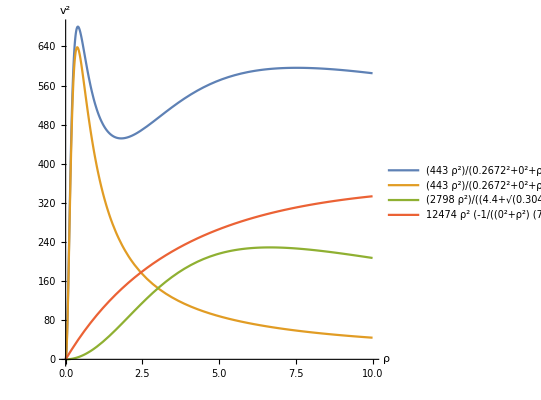

```mathematica
With[{z=0,G=1, Mb= 443, bb = 0.2672, Md = 2798, ad= 4.4, bd= 0.3048, Mh = 12474, ah= 7.7},Plot[{(G Mb ρ^2)/((bb^2+z^2+ρ^2)^(3/2))+(G Md ρ^2)/(((ad+√(bd^2+z^2))^2+ρ^2)^(3/2))+G Mh ρ^2 (-1/((z^2+ρ^2) (ah+√(z^2+ρ^2)))+Log[(ah+√(z^2+ρ^2))/ah]/((z^2+ρ^2)^(3/2))),(G Mb ρ^2)/((bb^2+z^2+ρ^2)^(3/2)),(G Md ρ^2)/(((ad+√(bd^2+z^2))^2+ρ^2)^(3/2)),G Mh ρ^2 (-1/((z^2+ρ^2) (ah+√(z^2+ρ^2)))+Log[(ah+√(z^2+ρ^2))/ah]/((z^2+ρ^2)^(3/2)))}, {ρ,0,10},AxesLabel->{"ρ","v^2"},AspectRatio->1,PlotLegends->"Expressions"]]
```

Velocidad circular solo DM (NFW)

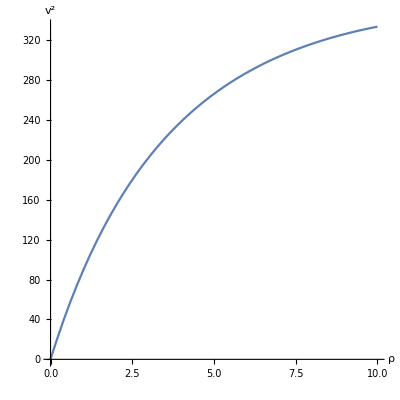

```mathematica
With[{z=0,G=1, Mb= 443, bb = 0.2672, Md = 2798, ad= 4.4, bd= 0.3048, Mh = 12474, ah= 7.7},Plot[{G Mh ρ^2 (-1/((z^2+ρ^2) (ah+√(z^2+ρ^2)))+Log[(ah+√(z^2+ρ^2))/ah]/((z^2+ρ^2)^(3/2)))}, {ρ,0,10},AxesLabel->{"ρ","v^2"},AspectRatio->1]]
```

Disc density  (from Miyamoto-Nagai potential)

```mathematica
Laplacian[-(G M)/(4π G Sqrt[ρ^2+(a + Sqrt[z^2 + b^2])^2]) ,{ρ,ϕ,z},"Cylindrical"]//Simplify
```

(b^2 M (a^3+5 a^2 √(b^2+z^2)+3 (b^2+z^2)^(3/2)+a (7 b^2+7 z^2+ρ^2)))/(4 π (b^2+z^2)^(3/2) ((a+√(b^2+z^2))^2+ρ^2)^(5/2))

Integral respecto a ρ

```mathematica
Simplify[-(a^3 b^2 M)/(12 π (b^2+z^2)^(3/2) ((a+√(b^2+z^2))^2+ρ^2)^(3/2))-(5 a^2 b^2 M)/(12 π (b^2+z^2) ((a+√(b^2+z^2))^2+ρ^2)^(3/2))-(b^2 M)/(4 π ((a+√(b^2+z^2))^2+ρ^2)^(3/2))+(a b^2 M (-2 a^2-4 a √(b^2+z^2)-3 (3 b^2+3 z^2+ρ^2)))/(12 π (b^2+z^2)^(3/2) ((a+√(b^2+z^2))^2+ρ^2)^(3/2))]
```

Ya integrada de 0 a ρ y ϕ de 0 a 2π y falta z de 0 a z

```mathematica
-b^2 M((a^3+3 a^2 √(b^2+z^2)+(b^2+z^2)^(3/2)+a (3 b^2+3 z^2+ρ^2))/((b^2+z^2)^(3/2) ((a+√(b^2+z^2))^2+ρ^2)^(3/2))-1/((b^2+z^2)^(3/2)))
```

```mathematica
Integrate[-1/((b^2+z^2)^(3/2)), z]
```

-z/(b^2 √(b^2+z^2))

```mathematica
Animate[Plot3D[(b^2 M (a^3+5 a^2 √(b^2+z^2)+3 (b^2+z^2)^(3/2)+a (7 b^2+7 z^2+ρ^2)))/(4 π (b^2+z^2)^(3/2) ((a+√(b^2+z^2))^2+ρ^2)^(5/2)),{z,-0.6,0.6},{ρ, 0, 0.6}, AxesLabel->Automatic],{a,0,0.533651},{b,0,2},{M,0,2},AnimationRunning->False]
```

Density Miyamoto-Nagai coordenadas cartesianas

```mathematica
TransformedField["Cylindrical"-> "Cartesian",(b^2 M (a^3+5 a^2 √(b^2+z^2)+3 (b^2+z^2)^(3/2)+a (7 b^2+7 z^2+ρ^2)))/(4 π (b^2+z^2)^(3/2) ((a+√(b^2+z^2))^2+ρ^2)^(5/2)),{ρ,ϕ,z}->{x,y,ζ}]//Simplify
```

(b^2 M (a^3+5 a^2 √(b^2+ζ^2)+3 (b^2+ζ^2)^(3/2)+a (7 b^2+x^2+y^2+7 ζ^2)))/(4 π (b^2+ζ^2)^(3/2) (x^2+y^2+(a+√(b^2+ζ^2))^2)^(5/2))

```mathematica
With[{r=70},Manipulate[DensityPlot3D[(b^2 M (a^3+5 a^2 √(b^2+ζ^2)+3 (b^2+ζ^2)^(3/2)+a (7 b^2+x^2+y^2+7 ζ^2)))/(4 π (b^2+ζ^2)^(3/2) (x^2+y^2+(a+√(b^2+ζ^2))^2)^(5/2)),{x,-r,r},{y,-r,r},{ζ,-r,r}],{a,10,40},{b,0.5,2},{M,5,20}]]
```

```mathematica
ρMN[x_,y_,ζ_,M_,a_,b_]:=(b^2 M (a^3+5 a^2 √(b^2+ζ^2)+3 (b^2+ζ^2)^(3/2)+a (7 b^2+x^2+y^2+7 ζ^2)))/(4 π (b^2+ζ^2)^(3/2) (x^2+y^2+(a+√(b^2+ζ^2))^2)^(5/2))
```

Disk density

```mathematica
With[{M= 222.49, b = .4, a = 25, rmax = 70},DensityPlot3D[ρMN[x,y,z,M,a,b], {x,-rmax,rmax}, {y,-rmax,rmax}, {z,-rmax,rmax}]]
```

-Graphics3D-

Bulge density

```mathematica
With[{M= 1.18, b =1, rmax = 3},DensityPlot3D[ρMN[x,y,z,M,0,b], {x,-rmax,rmax}, {y,-rmax,rmax}, {z,-rmax,rmax}]]
```

-Graphics3D-

Masa gaussian core

```mathematica
4π Mc/(Sqrt[π]^3 Rc^3) Integrate[Exp[-r^2/Rc^2] r^2, {r, 0,x}]
```

(Mc (-2 ⅇ^(-x^2/Rc^2) x+√π Rc Erf[x/Rc]))/(√π Rc)

aceleracion

```mathematica
(Mc  G(-2 ⅇ^(-x^2/Rc^2) x+√π Rc Erf[x/Rc]))/(√π Rc r^2)
```

(G Mc (-2 ⅇ^(-x^2/Rc^2) x+√π Rc Erf[x/Rc]))/(√π r^2 Rc)

Masa halo NFW + Gaussian core

```mathematica
Mh[r_, Mc_, Rc_, re_, rs_]:= 1/(√π Rc^3)Mc (Rc^2 (-2 ⅇ^(-re^2/Rc^2) re+√π Rc Erf[re/Rc]) HeavisideTheta[r-re]+Rc^2 (-2 ⅇ^(-r^2/Rc^2) r+√π Rc Erf[r/Rc]) HeavisideTheta[-r+re]+1/(r+rs)4 ⅇ^(-re^2/Rc^2) re (re+rs) HeavisideTheta[r-re] ((-r+re) rs+(r+rs) (re+rs) Log[(r+rs)/rs]-(r+rs) (re+rs) Log[(re+rs)/rs]))
```

```mathematica
With[{G = 43131.26},Animate[Plot[Sqrt[ G Mh[r, Mc, Rc, re, rs]/r] ,{r,0,20}, AxesLabel->{"r", "v_CoreNFW"},PlotRange->{0,360}, GridLines->{{Rc, rs, re, 2.3816 Rc},{Sqrt[(G Mc)/20],Sqrt[G Mc/Rc]}}],{Rc,10^-4,10^-1},{rs,1,15},{re,0.01,0.02}, {Mc, 0.001, 0.005},AnimationRunning->False]]
```

```mathematica
With[{G = 43131.26},Animate[Plot[Sqrt[ G Mh[r, Mc, Rc, re, rs]/r] ,{r,0,5}, AxesLabel->{"r", "v_CoreNFW"},PlotRange->{0,60}, GridLines->{{Rc, rs, re, 2.3816 Rc},{Sqrt[(G Mc)/20],Sqrt[G Mc/Rc]}}],{Rc,10^-1,1},{rs,1,15},{re,0.01,5}, {Mc, 0.001, 0.05},AnimationRunning->False]]
```

```mathematica
With[{G = 43131.26,  Rc = 0.006},Animate[LogLogPlot[Sqrt[ G Mh[r, Mc, Rc, re, rs]/r] ,{r,.001,102}, AxesLabel->{"r", "v_CoreNFW"},PlotRange->{.1,900}, GridLines->{{Rc, rs, re, 2.3816 Rc},{Sqrt[(G Mc)/20],Sqrt[G Mc/Rc]}}],{rs,1,15},{re,0.01,0.02}, {Mc, 0.001, 0.005},AnimationRunning->False]]
```

```mathematica
ρh[r_, Mc_, Rc_, re_, rs_]:=HeavisideTheta[re-r] Mc/(Rc^3 Sqrt[π]^3)Exp[-r^2/Rc^2]+ (Mc re)/(rs Rc^3 Sqrt[π]^3)  ⅇ^(-re^2/Rc^2) (1+re/rs)^2 HeavisideTheta[r-re] rs/(r(1+r/rs)^2)
Animate[Plot[ ρh[r, Mc, Rc, re, rs] ,{r,0,10}, AxesLabel->{"r", "ρ_CoreNFW"},GridLines->{{Rc, rs, re, 2.3816 Rc},{Mc,Mc/(Rc^3 Sqrt[π ]^3)}}],{Mc,0,20.},{Rc,2,5},{rs,1,100},{re,2,10},AnimationRunning->False]
```

```mathematica
Rc = 0.00499913
Mc = 0.0232453
re = 5.55468
rs = 3.8091
```

0.00499913

0.0232453

5.55468

3.8091

General::munfl: Exp[-1.23461×10^6] is too small to represent as a normalized machine number; precision may be lost.

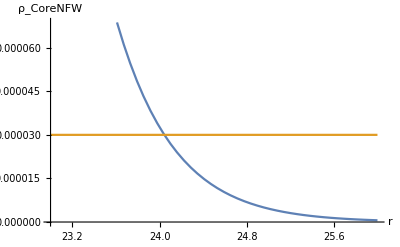

```mathematica
Plot[ {ρh[r, Mc*10^10, Rc*1000, re*1000, rs*1000],200 1.5 10^-7} ,{r,23,26}, AxesLabel->{"r", "ρ_CoreNFW"},GridLines->{{Rc, re},{Mc,Mc/(Rc^3 Sqrt[π ]^3)}}]
```

General::munfl: Exp[-1.23461×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.60062×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.23461×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

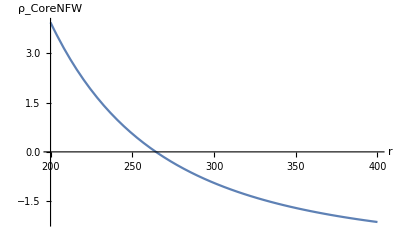

```mathematica
Plot[ {(3Mh[r, Mc*10^10, Rc, re, rs])/(4 π r^3)-200 1.5 10^-2} ,{r,200,400}, AxesLabel->{"r", "ρ_CoreNFW"}]
```

```mathematica
FindRoot[(3Mh[r, Mc*10^10, Rc, re, rs])/(4 π r^3)-200 1.5 10^-2,{r,260}]
```

General::munfl: Exp[-1.23461×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.70494×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{r→264.469}

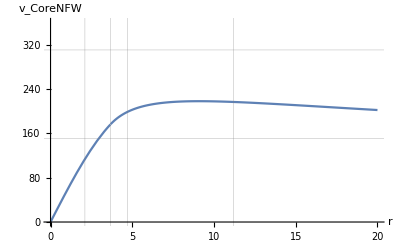

```mathematica
With[{Rc= 4.7,Mc = 10.5, re=3.67, rs= 2.1, G = 43131.26},Plot[Sqrt[ G Mh[r, Mc, Rc, re, rs]/r] ,{r,0,20}, AxesLabel->{"r", "v_CoreNFW"},PlotRange->{0,360}, GridLines->{{Rc, rs, re, 2.3816 Rc},{Sqrt[(G Mc)/20],Sqrt[G Mc/Rc]}}]]
```

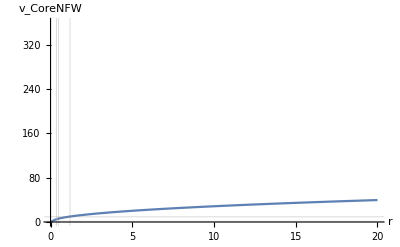

```mathematica
With[{Rc= 0.5,Mc = 0.001, re=0.374, rs= 423., G = 43131.26},Plot[Sqrt[ G Mh[r, Mc, Rc, re, rs]/r] ,{r,0,20}, AxesLabel->{"r", "v_CoreNFW"},PlotRange->{0,360}, GridLines->{{Rc, rs, re, 2.3816 Rc},{Sqrt[(G Mc)/20],Sqrt[G Mc/Rc]}}]]
```

```mathematica
Animate[Plot[ Mh[r, Mc, Rc, re, rs] ,{r,0,10}, AxesLabel->{"r", "M_CoreNFW"},GridLines->{{Rc, rs, re, 2.3816 Rc},{Mc,Mc/(Rc^3 Sqrt[π ]^3)}}],{Mc,0,20.},{Rc,2,5},{rs,1,100},{re,2,10},AnimationRunning->False]
```

```mathematica
ρh[r_, ρ0_, rs_]:=(rs ρ0)/(r(1+r/rs)^2)
Animate[Plot[ ρh[r, ρ0, rs] ,{r,0,10}, AxesLabel->{"r", "ρ_NFW"},GridLines->{{ rs},{ρ0,ρ0}}],{ρ0,2,5},{rs,1,20},AnimationRunning->False]
```

```mathematica
Assuming[{r>0, rs>0, x>0}, Integrate[(4 π rs ρ0)/(r(1+r/rs)^2)  r^2, {r,0,x}]]
```

4 π rs^3 ρ0 (-x/(rs+x)-Log[rs]+Log[rs+x])

```mathematica
Mh[x_, ρ0_, rs_]:=4 π rs^3 ρ0 (-x/(rs+x)-Log[rs]+Log[rs+x])
```

```mathematica
2 G Mh[r, ρ0, rs]/r
```

(8 G π rs^3 ρ0 (-r/(r+rs)-Log[rs]+Log[r+rs]))/r

```mathematica
With[{G = 43131.26},Animate[Plot[Sqrt[ G Mh[r, ρ0, rs]/r] ,{r,.001,50}, AxesLabel->{"r", "v_NFW"},PlotRange->{0,300}, GridLines->{{ rs, rs},{Sqrt[4 π G rs^2 ρ0(Log[2]- 1/2)],10}}],{ρ0,0.001,0.002},{rs,1,20},AnimationRunning->False]]
```

```mathematica
Solve[Mh[10^3, ρ0, 12]==6 10^11]
```

{{ρ0→-197656250000/(9 π (250+253 Log[12]-253 Log[1012]))}}

```mathematica
N[-197656250000/(9 π (250+253 Log[12]-253 Log[1012]))]
```

8.01682×10^6

```mathematica
Solve[Mh[10^3, ρ0, 12]==8 10^11]
```

{{ρ0→-790625000000/(27 π (250+253 Log[12]-253 Log[1012]))}}

```mathematica
N[-790625000000/(27 π (250+253 Log[12]-253 Log[1012]))]
```

1.06891×10^7

```mathematica
Solve[Mh[10^3, ρ0, 12]==10 10^11]
```

{{ρ0→-988281250000/(27 π (250+253 Log[12]-253 Log[1012]))}}

```mathematica
N[-988281250000/(27 π (250+253 Log[12]-253 Log[1012]))]
```

1.33614×10^7

Masa de Miyamoto Nagai

```mathematica
With[{M= 222.49, b = .4, a = 25, rmax = 70},NIntegrate[(b^2 M (a^3+5 a^2 √(b^2+z^2)+3 (b^2+z^2)^(3/2)+a (7 b^2+7 z^2+ρ^2)))/(4 π (b^2+z^2)^(3/2) ((a+√(b^2+z^2))^2+ρ^2)^(5/2))4 π ρ, {z,0,rmax}, {ρ, 0,rmax}]]
```

147.639

```mathematica
With[{M= 222.49, b = .4, a = 25, rmax = 70},NIntegrate[(b^2 M (a^3+5 a^2 √(b^2+z^2)+3 (b^2+z^2)^(3/2)+a (7 b^2+7 z^2+ρ^2)))/(4 π (b^2+z^2)^(3/2) ((a+√(b^2+z^2))^2+ρ^2)^(5/2))4 π ρ, {z,0,rmax/2}, {ρ, 0,rmax}]]
```

147.634

```mathematica
\[FreakedSmiley]
```

\[FreakedSmiley]

Doble exponential bulge

```mathematica
ρ2b[r_]:=Mi/(8π ai^3) Exp[-r/ai] + Mo/(8π ao^3) Exp[-r/ao]
```

```mathematica
4π Integrate[(Mi/(8π ai^3) Exp[-r/ai] + Mo/(8π ao^3) Exp[-r/ao]) r^2, {r,0,x}]
```

1/2 (2 Mi+2 Mo-(ⅇ^(-x/ai) Mi (2 ai^2+2 ai x+x^2))/ai^2-(ⅇ^(-x/ao) Mo (2 ao^2+2 ao x+x^2))/ao^2)

```mathematica
Simplify[1/2 (2 Mi+2 Mo-(ⅇ^(-x/ai) Mi (2 ai^2+2 ai x+x^2))/ai^2-(ⅇ^(-x/ao) Mo (2 ao^2+2 ao x+x^2))/ao^2)]
```

Mi+Mo-(ⅇ^(-x/ai) Mi (2 ai^2+2 ai x+x^2))/(2 ai^2)-(ⅇ^(-x/ao) Mo (2 ao^2+2 ao x+x^2))/(2 ao^2)

Exponential disk

```mathematica
2π Σ Integrate[ Exp[-r/a]  r, {r,0,x}]
```

2 a π (a-ⅇ^(-x/a) (a+x)) Σ

```mathematica
2π Σ Integrate[ Exp[-r/a]  r, {r,0,∞}]
```

ConditionalExpression[2 a^2 π Σ,Re[a]>0]

Potencial total (todas las componentes)

```mathematica
-(G Mb)/Sqrt[ρ^2+z^2 + bb^2]-(G Md1)/Sqrt[ρ^2+(ad1 + Sqrt[z^2 + bd1^2])^2]-(G Md2)/Sqrt[ρ^2+(ad2 + Sqrt[z^2 + bd2^2])^2]-(G Md3)/Sqrt[ρ^2+(ad3 + Sqrt[z^2 + bd3^2])^2]
```

-(G Mb)/(√(bb^2+z^2+ρ^2))-(G Md1)/(√((ad1+√(bd1^2+z^2))^2+ρ^2))-(G Md2)/(√((ad2+√(bd2^2+z^2))^2+ρ^2))-(G Md3)/(√((ad3+√(bd3^2+z^2))^2+ρ^2))

Fuerza (todas las componentes) en coordenadas cilindricas

```mathematica
Grad[-(G Mb)/Sqrt[ρ^2+z^2 + bb^2]-(G Md1)/Sqrt[ρ^2+(ad1 + Sqrt[z^2 + bd1^2])^2]-(G Md2)/Sqrt[ρ^2+(ad2 + Sqrt[z^2 + bd2^2])^2]-(G Md3)/Sqrt[ρ^2+(ad3 + Sqrt[z^2 + bd3^2])^2],{ρ,ϕ,z},"Cylindrical"]//Simplify
```

{G ρ (Mb/((bb^2+z^2+ρ^2)^(3/2))+Md1/(((ad1+√(bd1^2+z^2))^2+ρ^2)^(3/2))+Md2/(((ad2+√(bd2^2+z^2))^2+ρ^2)^(3/2))+Md3/(((ad3+√(bd3^2+z^2))^2+ρ^2)^(3/2))),0,G z (Mb/((bb^2+z^2+ρ^2)^(3/2))+(Md1 (ad1+√(bd1^2+z^2)))/(√(bd1^2+z^2) ((ad1+√(bd1^2+z^2))^2+ρ^2)^(3/2))+(Md2 (ad2+√(bd2^2+z^2)))/(√(bd2^2+z^2) ((ad2+√(bd2^2+z^2))^2+ρ^2)^(3/2))+(Md3 (ad3+√(bd3^2+z^2)))/(√(bd3^2+z^2) ((ad3+√(bd3^2+z^2))^2+ρ^2)^(3/2)))}

```mathematica
-Grad[-(G Mb)/Sqrt[ρ^2+z^2 + bb^2]-(G Md1)/Sqrt[ρ^2+(ad1 + Sqrt[z^2 + bd1^2])^2],{ρ,ϕ,z},"Cylindrical"]//Simplify
```

{G ρ (-Mb/((bb^2+z^2+ρ^2)^(3/2))-Md1/(((ad1+√(bd1^2+z^2))^2+ρ^2)^(3/2))),0,G z (-Mb/((bb^2+z^2+ρ^2)^(3/2))-(Md1 (ad1+√(bd1^2+z^2)))/(√(bd1^2+z^2) ((ad1+√(bd1^2+z^2))^2+ρ^2)^(3/2)))}

```mathematica
TransformedField[ "Cylindrical"->"Spherical",{G ρ (-Mb/((bb^2+z^2+ρ^2)^(3/2))-Md1/(((ad1+√(bd1^2+z^2))^2+ρ^2)^(3/2))),0,G z (-Mb/((bb^2+z^2+ρ^2)^(3/2))-(Md1 (ad1+√(bd1^2+z^2)))/(√(bd1^2+z^2) ((ad1+√(bd1^2+z^2))^2+ρ^2)^(3/2)))},{ρ,ϕ,z}->{r,θ, f}]//Simplify
```

{G r (Cos[θ]^2 (-Mb/((bb^2+r^2)^(3/2))-(Md1 (ad1+√(bd1^2+r^2 Cos[θ]^2)))/(√(bd1^2+r^2 Cos[θ]^2) (ad1^2+bd1^2+r^2+2 ad1 √(bd1^2+r^2 Cos[θ]^2))^(3/2)))+(-Mb/((bb^2+r^2)^(3/2))-Md1/((ad1^2+bd1^2+r^2+2 ad1 √(bd1^2+r^2 Cos[θ]^2))^(3/2))) Sin[θ]^2),(ad1 G Md1 r Cos[θ] Sin[θ])/(√(bd1^2+r^2 Cos[θ]^2) (ad1^2+bd1^2+r^2+2 ad1 √(bd1^2+r^2 Cos[θ]^2))^(3/2)),0}

```mathematica
Md={0.606,0.013,0.546,0.218};
ad={3.859,0.993,9.021,6.062} ;
bd={0.243,0.776,0.168,0.128};
Md1 = Md[[1]];
Md2 = Md[[2]];
Md3 = Md[[3]];
ad1 = ad[[1]];
ad2 = ad[[2]];
ad3 = ad[[3]];
bd1 = bd[[1]];
bd2 = bd[[2]];
bd3 = bd[[3]];
ab=0.;
Mb=0.8;
bb=0.22;
```

```mathematica
gh[r_,θ_]:=(1/(Exp[Sqrt[((G r)/gd)(Cos[θ]^2 (Mb/((bb^2+r^2)^(3/2))+(Md1 (ad1+√(bd1^2+r^2 Cos[θ]^2)))/(√(bd1^2+r^2 Cos[θ]^2) (ad1^2+bd1^2+r^2+2 ad1 √(bd1^2+r^2 Cos[θ]^2))^(3/2))+(Md2 (ad2+√(bd2^2+r^2 Cos[θ]^2)))/(√(bd2^2+r^2 Cos[θ]^2) (ad2^2+bd2^2+r^2+2 ad2 √(bd2^2+r^2 Cos[θ]^2))^(3/2))+(Md3 (ad3+√(bd3^2+r^2 Cos[θ]^2)))/(√(bd3^2+r^2 Cos[θ]^2) (ad3^2+bd3^2+r^2+2 ad3 √(bd3^2+r^2 Cos[θ]^2))^(3/2)))+(Mb/((bb^2+r^2)^(3/2))+Md1/((ad1^2+bd1^2+r^2+2 ad1 √(bd1^2+r^2 Cos[θ]^2))^(3/2))+Md2/((ad2^2+bd2^2+r^2+2 ad2 √(bd2^2+r^2 Cos[θ]^2))^(3/2))+Md3/((ad3^2+bd3^2+r^2+2 ad3 √(bd3^2+r^2 Cos[θ]^2))^(3/2))) Sin[θ]^2)]]-1))G r (Cos[θ]^2 (Mb/((bb^2+r^2)^(3/2))+(Md1 (ad1+√(bd1^2+r^2 Cos[θ]^2)))/(√(bd1^2+r^2 Cos[θ]^2) (ad1^2+bd1^2+r^2+2 ad1 √(bd1^2+r^2 Cos[θ]^2))^(3/2))+(Md2 (ad2+√(bd2^2+r^2 Cos[θ]^2)))/(√(bd2^2+r^2 Cos[θ]^2) (ad2^2+bd2^2+r^2+2 ad2 √(bd2^2+r^2 Cos[θ]^2))^(3/2))+(Md3 (ad3+√(bd3^2+r^2 Cos[θ]^2)))/(√(bd3^2+r^2 Cos[θ]^2) (ad3^2+bd3^2+r^2+2 ad3 √(bd3^2+r^2 Cos[θ]^2))^(3/2)))+(Mb/((bb^2+r^2)^(3/2))+Md1/((ad1^2+bd1^2+r^2+2 ad1 √(bd1^2+r^2 Cos[θ]^2))^(3/2))+Md2/((ad2^2+bd2^2+r^2+2 ad2 √(bd2^2+r^2 Cos[θ]^2))^(3/2))+Md3/((ad3^2+bd3^2+r^2+2 ad3 √(bd3^2+r^2 Cos[θ]^2))^(3/2))) Sin[θ]^2)
```

139.18

11.9897

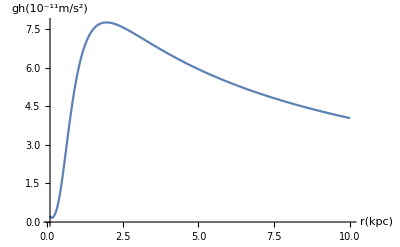

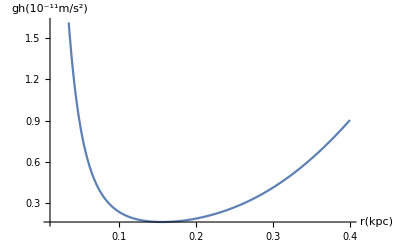

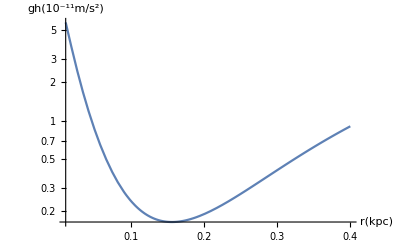

```mathematica
G=139.18
gd = .0861452 G
Plot[gh[r,π/2],{r,0.1,10},AxesLabel->{"r(kpc)","gh(10^-11m/s^2)"}]
Plot[gh[r,π/2],{r,0.01,0.4},AxesLabel->{"r(kpc)","gh(10^-11m/s^2)"}]
LogPlot[gh[r,π/2],{r,0.01,0.4},AxesLabel->{"r(kpc)","gh(10^-11m/s^2)"}]
```

```mathematica
gh[r,π/2]//Simplify
```

(139.18 r (0.8/((0.0484+r^2)^(3/2))+0.013/((3.12936+r^2)^(3/2))+0.606/((16.8264+r^2)^(3/2))+0.546/((84.4377+r^2)^(3/2))))/(-1+ⅇ^(3.4071 √(r (0.8/((0.0484+r^2)^(3/2))+0.013/((3.12936+r^2)^(3/2))+0.606/((16.8264+r^2)^(3/2))+0.546/((84.4377+r^2)^(3/2))))))

```mathematica
Grad[-(G Mb)/Sqrt[r^2 + bb^2],{r,θ,ϕ},"Spherical"]//Simplify
```

{(G Mb r)/((bb^2+r^2)^(3/2)),0,0}

Aceleraciones con parametros efectivos

```mathematica
Md={0.606,0.013,0.546,0.218};
ad={3.859,0.993,9.021,6.062} ;
bd={0.243,0.776,0.168,0.128};
Md1 = Md[[1]];
Md2 = Md[[2]];
Md3 = Md[[3]];
ad1 = ad[[1]];
ad2 = ad[[2]];
ad3 = ad[[3]];
bd1 = bd[[1]];
bd2 = bd[[2]];
bd3 = bd[[3]];
ab=0.;
Mb=0.8;
bb=0.22;
ghh[r_]:=((G Mb r)/((bb^2+r^2)^(3/2))+ (G Md1 r)/(((ad1+bd1)^2+r^2)^(3/2))+ (G Md2 r)/(((ad2+bd2)^2+r^2)^(3/2))+ (G Md3 r)/(((ad3+bd3)^2+r^2)^(3/2)))/(Exp[Sqrt[(1/gd)((G Mb r)/((bb^2+r^2)^(3/2))+ (G Md1 r)/(((ad1+bd1)^2+r^2)^(3/2))+ (G Md2 r)/(((ad2+bd2)^2+r^2)^(3/2))+ (G Md3 r)/(((ad3+bd3)^2+r^2)^(3/2)))]]-1)
```

```mathematica
G=139.18
gd = .0861452 G
Plot[ghh[r],{r,0.1,10},AxesLabel->{"r(kpc)","gh(10^-11m/s^2)"}]
Plot[ghh[r],{r,0.01,0.4},AxesLabel->{"r(kpc)","gh(10^-11m/s^2)"}]
LogPlot[ghh[r],{r,0.01,0.4},AxesLabel->{"r(kpc)","gh(10^-11m/s^2)"}]
```

139.18

11.9897

-Graphics-

-Graphics-

-Graphics-